```mathematica
spherePoint[dim_]:=Table[RandomVariate[NormalDistribution[]],dim]//Normalize;
```

```mathematica
randomPointInBall[dim_]:=spherePoint[dim]*RandomReal[]^(1/dim);
```

```mathematica
zeroInsideSimplex[vertices_]:=Module[{m=#-Last[vertices]&/@Most[vertices],lastVertexNewCoords},
lastVertexNewCoords=-Last[vertices].Inverse[m];
AllTrue[lastVertexNewCoords,#>=0&]&&Total[lastVertexNewCoords]<=1
];
```

```mathematica
feasibilifySimplex[vertices_]:=Module[{m=#-Last[vertices]&/@Most[vertices],lastVertexNewCoords,multipliers},
lastVertexNewCoords=-Last[vertices].Inverse[m];
multipliers=Append[If[#>=0,1,-1]&/@lastVertexNewCoords,If[Total[lastVertexNewCoords]<=1,1,-1]];
vertices*multipliers
];
```

```mathematica
generateSimplexWithZeroInside[dim_]:=feasibilifySimplex[Table[spherePoint[dim],dim+1]];
```

```mathematica
exportSimplexInBallExample[dim_,filename_]:=Module[
{vertices=generateSimplexWithZeroInside[dim],openAppend=OpenAppend[filename],delta},
(*delta=-SignedRegionDistance[Simplex[vertices],Table[0,dim]]//N;*)
Export[openAppend,"# first line is delta, then "<>ToString[dim+1]<>" lines with vertices\n","Text"];
Export[openAppend,ToString["delta"]<>"\n","Text"];
Export[openAppend,vertices,"CSV"];
Close[openAppend];
];
```

```mathematica
exportSimplexPlusBallInBallExample[dim_,filename_]:=Module[
{vertices=generateSimplexWithZeroInside[dim],openAppend=OpenAppend[filename],delta,radius=RandomReal[]},
(*delta=N[-SignedRegionDistance[Simplex[vertices],Table[0,dim]]];*)
Export[openAppend,"# A = simplex + ball, B = unit ball, t = 1, x = 0\n","Text"];
Export[openAppend,"# first line is the radius of the ball, second line is delta, then "<>ToString[dim+1]<>" lines with vertices of the simplex\n","Text"];
Export[openAppend,ToString[NumberForm[radius,16]]<>"\n","Text"];
Export[openAppend,ToString["delta"]<>"\n","Text"];
Export[openAppend,vertices*(1-radius),"CSV"];
Close[openAppend];
];
```

```mathematica
exportDegenerateSimplexInBallExample[dim_,filename_]:=Module[
{vertices=generateSimplexWithZeroInside[dim-1],openAppend=OpenAppend[filename]},
Export[openAppend,"# "<>ToString[dim]<>" lines with vertices\n","Text"];
Export[openAppend,Table[PrependTo[vertices[[i]],0],{i,dim}],"CSV"];
Close[openAppend];
];
```

```mathematica
exportPolyhedronInBallExample[dim_,filename_]:=Module[
{basedVertices=generateSimplexWithZeroInside[dim],restVertices=Table[randomPointInBall[dim],{dim+1}],openAppend=OpenAppend[filename]},
Export[openAppend,"# the first line is minimal distance from non-based vertices to the sphere, then "<>ToString[2*(dim+1)]<>" lines with vertices\n","Text"];
Export[openAppend,ToString[NumberForm[Min[(1-Norm[#])&/@restVertices],16]]<>"\n","Text"];
Export[openAppend,Join[basedVertices,restVertices],"CSV"];
Close[openAppend];
];
```

```mathematica
reflection[y_,x_]:=With[{normal=Normalize[Normalize[x]-Prepend[Table[0,Length[x]-1],1]]},y-2normal*(normal.y)];
```

```mathematica
generateTouchingEllipsoid[x_]:=Transpose[reflection[#,x]&/@DiagonalMatrix[Prepend[Table[RandomReal[],Length[x]-1],1]]*(1-Norm[x])];
```

```mathematica
exportPerturbedSimplexExample[dim_,filename_]:=Module[
{vertices=feasibilifySimplex[Table[randomPointInBall[dim],dim+1]],
stream=OpenWrite[filename],
matrices},
vertices=If[Norm[#]>0.5,#,Normalize[#]/2]&/@vertices;
matrices=generateTouchingEllipsoid/@vertices;
Export[stream,"# the first "<>ToString[dim+1]<>" lines are the centers of the ellipsoids\n","Text"];Export[stream,"# then "<>ToString[(dim+1)^2]<>" lines with the matrices that map the unit ball into the corresponding ellipsoid\n","Text"];
Export[stream,vertices,"CSV"];
Export[stream,Join@@matrices,"CSV"];
Close[stream];
];
```

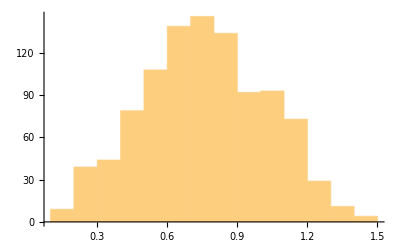

```mathematica
minEdge[simplex_]:=Min[Norm[#[[1]]-#[[2]]]&/@Subsets[simplex,{2}]];
Histogram[ minEdge/@Table[feasibilifySimplex[Table[randomPointInBall[2],3]],1000]]
```

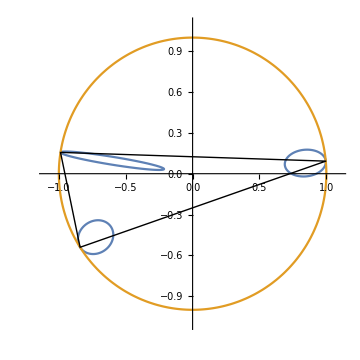

```mathematica
vertices=feasibilifySimplex[Table[randomPointInBall[2],3]];
matrices=generateTouchingEllipsoid/@vertices;
Show[
ParametricPlot[{
Table[vertices[[i]]+matrices[[i]].{Cos[t],Sin[t]},{i,3}],
{Cos[t],Sin[t]}
},{t,0,2π},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],
Graphics[{Line[Normalize/@Append[vertices,First[vertices]]]}]
]
```

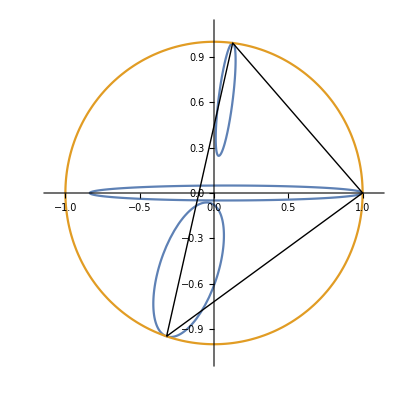

```mathematica
vertices={{-0.17079643722853244,-0.5074179216575105},{0.08237810634892805,0.000025455468701732736},{0.07844687669310187,0.6189856278351076}};
matrices={{{-0.148215620865378,-0.1856482049470853},
{-0.44033273478683493,0.062489026558735505}},
{{0.9176218459081976,0.00001525759803144801},
{0.0002835522112237442,-0.049376110344260336}},
{{0.047282007622567936,0.04732928719950622},
{0.37307901101093915,-0.005998256809124409}}};
Show[
ParametricPlot[{
Table[vertices[[i]]+matrices[[i]].{Cos[t],Sin[t]},{i,3}],
{Cos[t],Sin[t]}
},{t,0,2π},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],
Graphics[{Line[Normalize/@Append[vertices,First[vertices]]]}]
]
```

```mathematica
Do[
exportPerturbedSimplexExample[100,NotebookDirectory[]<>"tests/100d/perturbed-simplex-in-ball/"<>ToString[n]],{n,100}]
```